```mathematica
VectorPlot
```

VectorPlot

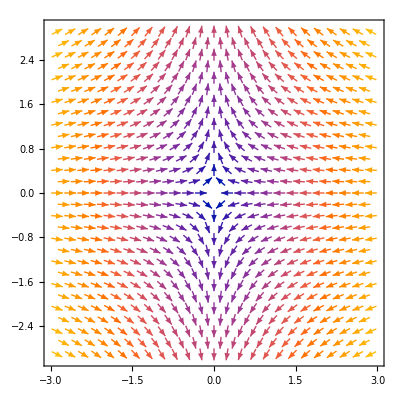

```mathematica
VectorPlot[{-i,1/2*j},{i,-3,3},{j,-3,3},VectorPoints->Fine]
```

```mathematica
(*Manipulate[VectorPlot[{a*i,-1*b*j},{i,-3,3},{j,-3,3},VectorPoints->Fine],{{a,-.01,.01},{b,-0.01,.01}}]*)
```

```mathematica
(*Manipulate[VectorPlot[{a*x,b*y},{x,-3,3},{y,-3,3},VectorPoints->20,Axes->True,AxesLabel->{x,y}],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
Manipulate[Show[VectorPlot[{a*x,b*y},{x,-3,3},{y,-3,3}],ContourPlot[a*x+b*y,{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
Manipulate[Show[VectorPlot[{a*x,b*y},{x,-3,3},{y,-3,3}],ContourPlot[0.5*a*x^2+0.5*b*y^2,{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
f[x_,y_,a_,b_]:=0.5*a*x^2+0.5*b*y^2
gradF[x_,y_,a_,b_]:=Evaluate[Grad[f[u,v,a,b],{u,v}]/. {u->x,v->y}]

Manipulate[Show[VectorPlot[gradF[x,y,a,b],{x,-3,3},{y,-3,3}],ContourPlot[f[x,y,a,b],{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
f[x_,y_,a_,b_]:=0.5*a*x^2+0.5*b*y^2
gradF[x_,y_,a_,b_]:=Evaluate[Grad[f[u,v,a,b],{u,v}]/. {u->x,v->y}]

Manipulate[Show[VectorPlot[gradF[x,y,a,b],{x,-3,3},{y,-3,3}],ContourPlot[f[x,y,a,b],{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],PlotLabel->Grid[{{"Function:",f[x,y,a,b]},{"Gradient:",gradF[x,y,a,b]}}],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
f[x_,y_,a_,b_]:=a*x+0.5*y^2
gradF[x_,y_,a_,b_]:=Evaluate[Grad[f[u,v,a,b],{u,v}]/. {u->x,v->y}]

Manipulate[Show[VectorPlot[gradF[x,y,a,b],{x,-3,3},{y,-3,3}],ContourPlot[f[x,y,a,b],{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],PlotLabel->Grid[{{"Function:",f[x,y,a,b]},{"Gradient:",gradF[x,y,a,b]}}],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
(*Define the vector field*)vectorField={y,-x};

(*Integrate the vector field*)
sol=DSolve[{D[f[x,y],x]==vectorField[[1]],D[f[x,y],y]==vectorField[[2]]},f[x,y],{x,y}];

(*Extract the solution*)
potentialFunction=f[x,y]/. sol[[1]];

(*Plot the vector field and level curves of the potential function*)
Manipulate[Show[VectorPlot[vectorField,{x,-3,3},{y,-3,3}],ContourPlot[potentialFunction,{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

ReplaceAll::reps: {f^(1,0)[x,y]==y,f^(0,1)[x,y]==-x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
f[x_,y_,a_,b_]:=0.5*a*x^2+0.5*b*y^2
(*gradF[x_,y_,a_,b_]:=Evaluate[Grad[f[u,v,a,b],{u,v}]/. {u->x,v->y}]*)
Manipulate[Show[VectorPlot[f[x_,y_,a_,b_],{x,-3,3},{y,-3,3}],(*ContourPlot[f[x,y,a,b],{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],*)PlotLabel->Grid[{(*{"Function:",f[x,y,a,b]},*){"Gradient:",f[x,y,a_,b_]}}],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
f[x_,y_,a_,b_]:=0.5*a*x^2+0.5*b*y^2
(*gradF[x_,y_,a_,b_]:=Evaluate[Grad[f[u,v,a,b],{u,v}]/. {u->x,v->y}]*)
Manipulate[Show[VectorPlot[gradF[x,y,a,b],{x,-3,3},{y,-3,3}],(*ContourPlot[f[x,y,a,b],{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],*)PlotLabel->Grid[{(*{"Function:",f[x,y,a,b]},*){"Gradient:",gradF[x,y,a,b]}}],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
f[x_,y_,a_,b_]:=a*2x-b*y
(*gradF[x_,y_,a_,b_]:=Evaluate[Grad[f[u,v,a,b],{u,v}]/. {u->x,v->y}]*)
Manipulate[Show[VectorPlot[f[x_,y_,a_,b_],{x,-3,3},{y,-3,3}],(*ContourPlot[f[x,y,a,b],{x,-3,3},{y,-3,3},Contours->10,ColorFunction->"TemperatureMap",ContourShading->None],*)PlotLabel->Grid[{(*{"Function:",f[x,y,a,b]},*){"Gradient:",f[x,y,a_,b_]}}],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
f[x_,y_,a_,b_]:=a*x+-b*y
Manipulate[Show[VectorPlot[f[x,y,a,b],{x,-3,3},{y,-3,3}],PlotLabel->Grid[{{"Function:",f[x,y,a,b]},{"Gradient:",f[x,y,a,b]}}],PlotRange->All],{a,-2,2,0.1},{b,-2,2,0.1}]
```

```mathematica
(*Problem two*)
vecFunc[x_,y_,a_,b_,c_]:={a*c*2x,b*c*-y}

Manipulate[VectorPlot[vecFunc[x,y,a,b,c],{x,-3,3},{y,-3,3},VectorColorFunction->Automatic,VectorScale->Small,PlotRange->All,PlotLabel->"Vector field: ("<>ToString[a]<>"x, "<>ToString[b]<>"y)"<>ToString[a]<>"c)"],{a,-2,2,0.1},{b,-2,2,0.1},{c,-2,2,0.1}]
```

```mathematica
(*Problem three*)
vecFunc[x_,y_,a_,b_,c_]:={a*c*x,b*c*1/2*y}
Manipulate[VectorPlot[vecFunc[x,y,a,b,c],{x,-3,3},{y,-3,3},VectorColorFunction->Automatic,VectorScale->Small,PlotRange->All,PlotLabel->"Vector field: ("<>ToString[a]<>"x, "<>ToString[b]<>"y)"<>ToString[a]<>"c)"],{a,-2,2,0.1},{b,-2,2,0.1},{c,-2,2,0.1}]
```

```mathematica
Manipulate[Module[{vector={x,y,z}},Graphics3D[{Red,Arrow[{{0,0,0},vector}],Text[vector,vector,{1,1,1}]},Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-10,10},{-10,10},{-10,10}}]],{x,-10,10},{y,-10,10},{z,-10,10}]
```

```mathematica
Manipulate[Module[{vector={x,y,z}},Graphics3D[{Red,Arrow[{{0,0,0},vector}],Text[vector,vector+{1,1,1}]},Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-10,10},{-10,10},{-10,10}}]],{x,-10,10},{y,-10,10},{z,-10,10}]
```

```mathematica
Manipulate[Module[{vector={x,y,z}},Panel[Column[{Graphics3D[{Red,Arrow[{{0,0,0},vector}]},Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-10,10},{-10,10},{-10,10}}],"Vector components: ","X: "<>ToString[x],"Y: "<>ToString[y],"Z: "<>ToString[z]}]]],{x,-10,10},{y,-10,10},{z,-10,10}]
```

```mathematica
Circle3D[center_,radius_,normal_]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},center],#]&,Map[Append[#,Last@center]&,#]&,Append[DeleteDuplicates[Most[#]],First[#]]&,Map[center+radius {Cos[#],Sin[#],0}&,Range[0,2 π,0.1]]][]

Arrow3D[{pt1_,pt2_},opts:OptionsPattern[]]:=Arrow[Tube[{pt1,pt2},0.02],opts]
```

```mathematica
Manipulate[Module[{loop1Center={0,0,-1},loop2Center={0,0,1},loopRadius=1,vector1,vector2},vector1=point-loop1Center;
vector2=loop2Center-point;
Panel[Column[{Graphics3D[{{Blue,Circle3D[loop1Center,loopRadius,{0,0,1}]},{Blue,Arrow3D[loop1Center,loop1Center+{loopRadius,0,-1}],Arrow3D[loop1Center,loop1Center+{-loopRadius,0,-1}]},{Green,Circle3D[loop2Center,loopRadius,{0,0,1}]},{Green,Arrow3D[loop2Center,loop2Center+{loopRadius,0,1}],Arrow3D[loop2Center,loop2Center+{-loopRadius,0,1}]},{Red,Arrow3D[loop1Center,point]},{Red,Arrow3D[point,loop2Center]}},Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-2,2},{-2,2},{-2,2}}],"Vector 1 components: ","X: "<>ToString[vector1[[1]]],"Y: "<>ToString[vector1[[2]]],"Z: "<>ToString[vector1[[3]]],"Vector 2 components: ","X: "<>ToString[vector2[[1]]],"Y: "<>ToString[vector2[[2]]],"Z: "<>ToString[vector2[[3]]]}]]],{{point,{0,0,0}},{-2,-2,-2},{2,2,2}}]
```

```mathematica
Circle3D[center_,radius_,normal_]:=ParametricPlot3D[center+radius Cos[θ] Cross[normal,{1,0,0}]+radius Sin[θ] normal,{θ,0,2 π},PlotStyle->Thick,Axes->False]
```

```mathematica
Manipulate[Module[{loop1Center={0,0,-1},loop2Center={0,0,1},loopRadius=1,vector1,vector2},vector1=point-loop1Center;
vector2=loop2Center-point;
Panel[Column[{Show[Circle3D[loop1Center,loopRadius,{0,0,1}],Circle3D[loop2Center,loopRadius,{0,0,1}],Graphics3D[{{Red,Arrow[{loop1Center,point}]},{Red,Arrow[{point,loop2Center}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-2,2},{-2,2},{-2,2}}],"Vector 1 components: ","X: "<>ToString[vector1[[1]]],"Y: "<>ToString[vector1[[2]]],"Z: "<>ToString[vector1[[3]]],"Vector 2 components: ","X: "<>ToString[vector2[[1]]],"Y: "<>ToString[vector2[[2]]],"Z: "<>ToString[vector2[[3]]]}]]],{{point,{0,0,0}},{-2,-2,-2},{2,2,2}}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{0,0,-1},1,{0,0,1}],Circle3D[{0,0,1},1,{0,0,1}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-2,2},{-2,2},{-2,2}}].

```mathematica
Manipulate[Module[{loop1Center={0,0,-2},loop2Center={0,0,2},loopRadius=1,vector1,vector2},vector1=point-loop1Center;
vector2=loop2Center-point;
Panel[Column[{Show[Circle3D[loop1Center,loopRadius,{0,0,1}],Circle3D[loop2Center,loopRadius,{0,0,1}],Graphics3D[{{Red,Arrow[{loop1Center,point}]},{Red,Arrow[{point,loop2Center}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-2,2},{-2,2},{-4,4}}],"Vector 1 components: ","X: "<>ToString[vector1[[1]]],"Y: "<>ToString[vector1[[2]]],"Z: "<>ToString[vector1[[3]]],"Vector 2 components: ","X: "<>ToString[vector2[[1]]],"Y: "<>ToString[vector2[[2]]],"Z: "<>ToString[vector2[[3]]]}]]],{{point,{0,0,0}},{-2,-2,-4},{2,2,4}}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{0,0,-2},1,{0,0,1}],Circle3D[{0,0,2},1,{0,0,1}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-2,2},{-2,2},{-4,4}}].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,vector1,vector2},vector1=point-loop1Center;
vector2=loop2Center-point;
Panel[Column[{Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Center,point}]},{Red,Arrow[{point,loop2Center}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}}],"Vector 1 components: ","X: "<>ToString[vector1[[1]]],"Y: "<>ToString[vector1[[2]]],"Z: "<>ToString[vector1[[3]]],"Vector 2 components: ","X: "<>ToString[vector2[[1]]],"Y: "<>ToString[vector2[[2]]],"Z: "<>ToString[vector2[[3]]]}]]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{2,0,0},1,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}}].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,loop1Point,loop2Point},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
Panel[Column[{Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}]},{Red,Arrow[{point,loop2Point}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}}],"Vector 1 components: ","X: "<>ToString[point[[1]]-loop1Point[[1]]],"Y: "<>ToString[point[[2]]-loop1Point[[2]]],"Z: "<>ToString[point[[3]]-loop1Point[[3]]],"Vector 2 components: ","X: "<>ToString[loop2Point[[1]]-point[[1]]],"Y: "<>ToString[loop2Point[[2]]-point[[2]]],"Z: "<>ToString[loop2Point[[3]]-point[[3]]]}]]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}},{θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{2,0,0},1,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}}].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius=0.2},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Panel[Column[{Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}],Arrow[{point,loop2Point}]},{Blue,Arrow[{point,point+vector2x}],Arrow[{point+vector2x,point+vector2}]},{Green,Cone[{point,point+{0,0,coneRadius}},coneRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}}],"Vector 1 components: ","X: "<>ToString[point[[1]]-loop1Point[[1]]],"Y: "<>ToString[point[[2]]-loop1Point[[2]]],"Z: "<>ToString[point[[3]]-loop1Point[[3]]],"Vector 2 components: ","X: "<>ToString[vector2[[1]]],"Y: "<>ToString[vector2[[2]]],"Z: "<>ToString[vector2[[3]]]}]]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}},{θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{2,0,0},1,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}}].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius=0.2},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}]},{Green,Cone[{point,point+{0,0,coneRadius}},coneRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}},{θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{2,0,0},1,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius=0.2},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}]},{Green,Cone[{loop2Point,point},coneRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}},{θ1,0,2 π,π/16},{θ2,0,2 π,π/16}}]
```

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius=0.2},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}]},{Green,Cone[{loop2Center,point},loopRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}},{θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{2,0,0},1,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={2,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius=0.2},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Show[Circle3D[loop1Center,loopRadius,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}]},{Green,Opacity[0.5],Cone[{loop2Center,point},loopRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-4,-2,-2},{4,2,2}},{θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{2,0,0},1,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius,dist,magField},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}]},{Green,Opacity[0.5],Cone[{point,loop2Center},coneRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],(*Control the position of the point along the x-axis*){{point,{0,0,0}},{-4,0,0},{4,0,0}},(*Control the position on the loops*){θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector2,vector2x,vector2y,coneRadius,dist,magField},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}]},{Green,Opacity[0.5],Cone[{loop2Center,point},coneRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],(*Control the position of the point along the x-axis*){{point,{0,0,0}},{-4,0,0},{4,0,0}},(*Control the position on the loops*){θ1,0,2 π,π/16},{θ2,0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector1,vector2,vector2x,vector2y,coneRadius,dist,magField,tangentialVector},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector1=point-loop1Point;
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
(*Define the tangential vector at the end of Vector 1*)tangentialVector=loop1Center+{0,-loopRadius Sin[θ1],loopRadius Cos[θ1]};
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}],Arrow[{loop1Point,tangentialVector}],Text["Tangential Vector",loop1Point+0.5*(tangentialVector-loop1Point),{-1,-1}]},{Green,Opacity[0.5],Cone[{loop2Center,point},coneRadius]},{Black,Dashed,Line[{{-4,0,0},{4,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-4,4},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-3,-2,-2},{3,2,2}},{{θ1,0},0,2 π,π/16},{{θ2,0},0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-4,4},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector1,vector2,vector2x,vector2y,coneRadius,dist,magField,tangentialVector,tangentialDirection},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector1=point-loop1Point;
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
(*Define the tangential vector at the end of Vector 1*)tangentialDirection={-Sin[θ1],Cos[θ1]};
tangentialVector=loop1Point+tangentialDirection;
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}],Arrow[{loop1Point,tangentialVector}],Text["Tangential Vector",loop1Point+0.5*(tangentialVector-loop1Point),{-1,-1}]},{Green,Cone[{loop2Center,loop2Center+magField*{1,0,0}},coneRadius]},{Black,Dashed,Line[{{-3,0,0},{3,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-3,3},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-3,-2,-2},{3,2,2}},{{θ1,0},0,2 π,π/16},{{θ2,0},0,2 π,π/16}]
```

Thread::tdlen: Objects of unequal length in {-2,1,0}+{0,1} cannot be combined.

Thread::tdlen: Objects of unequal length in {0,1}+{-2,1,0}+{2,-1,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-3,3},{-2,2},{-2,2}},ImageSize→Large].

Thread::tdlen: Objects of unequal length in {-2,1,0}+{0,1} cannot be combined.

Thread::tdlen: Objects of unequal length in {0,1}+{-2,1,0}+{2,-1,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-3,3},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector1,vector2,vector2x,vector2y,coneRadius,dist,magField,tangentialVector,tangentialDirection},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector1=point-loop1Point;
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
(*Define the tangential vector at the end of Vector 1*)tangentialDirection={-vector1[[3]],vector1[[2]],0};
tangentialVector=loop1Point+tangentialDirection;
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}],Arrow[{loop1Point,tangentialVector}],Text["Tangential Vector",loop1Point+0.5*(tangentialVector-loop1Point),{-1,-1}]},{Green,Cone[{loop2Center,loop2Center+magField*{1,0,0}},coneRadius]},{Black,Dashed,Line[{{-3,0,0},{3,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-3,3},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-3,-2,-2},{3,2,2}},{{θ1,0},0,2 π,π/16},{{θ2,0},0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-3,3},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector1,vector2,vector2x,vector2y,coneRadius,dist,magField,tangentialVector,tangentialDirection},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector1=point-loop1Point;
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
(*Define the tangential vector at the end of Vector 1*)tangentialDirection={vector1[[3]],-vector1[[2]],0};
tangentialVector=loop1Point+tangentialDirection;
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}],Arrow[{loop1Point,tangentialVector}],Text["Tangential Vector",loop1Point+0.5*(tangentialVector-loop1Point),{-1,-1}]},{Green,Cone[{loop2Center,loop2Center+magField*{1,0,0}},coneRadius]},{Black,Dashed,Line[{{-3,0,0},{3,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-3,3},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-3,-2,-2},{3,2,2}},{{θ1,0},0,2 π,π/16},{{θ2,0},0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-3,3},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector1,vector2,vector2x,vector2y,coneRadius,dist,magField,tangentialVector,tangentialDirection},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];(*Distance from loop to point*)(*Simple model for magnetic field magnitude:proportional to 1/dist*)magField=1/dist;
(*Scale the size of the loop2 and the cone according to magField*)loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};(*Move loop2*)loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector1=point-loop1Point;
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
(*Define the tangential vector at the end of Vector 1*)tangentialDirection=-{vector1[[3]],-vector1[[2]],0};
tangentialVector=loop1Point+tangentialDirection;
Show[Circle3D[loop1Center,1,{0,1,0}],(*Loop1:fixed size*)Circle3D[loop2Center,loopRadius,{0,1,0}],(*Loop2:size varies*)Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}],Arrow[{loop1Point,tangentialVector}],Text["Tangential Vector",loop1Point+0.5*(tangentialVector-loop1Point),{-1,-1}]},{Green,Cone[{loop2Center,loop2Center+magField*{1,0,0}},coneRadius]},{Black,Dashed,Line[{{-3,0,0},{3,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-3,3},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-3,-2,-2},{3,2,2}},{{θ1,0},0,2 π,π/16},{{θ2,0},0,2 π,π/16}]
```

Show::gcomb: Could not combine the graphics objects in Show[Circle3D[{-2,0,0},1,{0,1,0}],Circle3D[{1/2,0,0},1/2,{0,1,0}],,Axes→True,AxesLabel→{X,Y,Z},PlotRange→{{-3,3},{-2,2},{-2,2}},ImageSize→Large].

```mathematica
μ0=4 π 10^-7;
I0=1;(*Assume some current*)ε=LeviCivitaTensor[3];
r={x,y,z};
integrand=Simplify[Sum[I0 ε[[i,j,k]] {Cos[θ],Sin[θ],0}[[j]] (r-{Cos[θ],Sin[θ],0})[[k]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2),{j,1,3},{k,1,3}],{i,1,3}];
Bfield=μ0/(4π)*Integrate[integrand,{θ,0,2 π}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Simplify::bass: 1 is not a well-formed assumption.

Simplify::bass: 3 is not a well-formed assumption.

Part::pkspec1: The expression True cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

1/10000000 if 
 |  |  |  |

```mathematica
μ0=4 π 10^-7;
I0=1;(*Assume some current*)ε=LeviCivitaTensor[3];
r={x,y,z};
Bfield=Table[μ0/(4π)*Integrate[Simplify[Sum[I0 ε[[i,j,k]] {Cos[θ],Sin[θ],0}[[j]] (r-{Cos[θ],Sin[θ],0})[[k]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2),{j,1,3},{k,1,3}]],{θ,0,2 π}],{i,1,3}]
```

{(z (-(-2 5 √((x 1)/1)+63+1)/(2 7 (1-2 x^2+6+2 x^2 z^2+2 y^2 z^2+z^4))+1))/10000000 if ,-(z (-1/(2 8 (1))+1/1))/10000000 if ,0}
 |  |  |  |

```mathematica
μ0=4 π 10^-7;
I0=1;(*Assume some current*)ε=LeviCivitaTensor[3];
r={x,y,z};

integrand=Table[Simplify[Sum[I0 *ε[[i,j,k]] {Cos[θ],Sin[θ],0}[[j]] (r-{Cos[θ],Sin[θ],0})[[k]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2),{j,1,3},{k,1,3}]],{i,1,3}]
```

{(z Sin[θ])/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2)),-(z Cos[θ])/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2)),(y Cos[θ]-x Sin[θ])/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2))}

```mathematica
μ0=4 π 10^-7;
I0=1;(*Assume some current*)ε=LeviCivitaTensor[3];
r={x,y,z};

integrandX=I0*ε[[1,2,3]] {Cos[θ],Sin[θ],0}[[2]] (r-{Cos[θ],Sin[θ],0})[[3]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2)+I0*ε[[1,3,2]] {Cos[θ],Sin[θ],0}[[3]] (r-{Cos[θ],Sin[θ],0})[[2]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2);

integrandY=I0*ε[[2,3,1]] {Cos[θ],Sin[θ],0}[[3]] (r-{Cos[θ],Sin[θ],0})[[1]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2)+I0*ε[[2,1,3]] {Cos[θ],Sin[θ],0}[[1]] (r-{Cos[θ],Sin[θ],0})[[3]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2);

integrandZ=I0*ε[[3,1,2]] {Cos[θ],Sin[θ],0}[[1]] (r-{Cos[θ],Sin[θ],0})[[2]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2)+I0*ε[[3,2,1]] {Cos[θ],Sin[θ],0}[[2]] (r-{Cos[θ],Sin[θ],0})[[1]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2);
```

```mathematica
μ0=4 π 10^-7;
I0=1;(*Assume some current*)r={x,y,z};

integrandX=I0*(-1)*{Cos[θ],Sin[θ],0}[[2]] (r-{Cos[θ],Sin[θ],0})[[3]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2)+I0*1*{Cos[θ],Sin[θ],0}[[3]] (r-{Cos[θ],Sin[θ],0})[[2]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2);

integrandY=I0*1*{Cos[θ],Sin[θ],0}[[3]] (r-{Cos[θ],Sin[θ],0})[[1]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2)+I0*(-1)*{Cos[θ],Sin[θ],0}[[1]] (r-{Cos[θ],Sin[θ],0})[[3]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2);

integrandZ=I0*(-1)*{Cos[θ],Sin[θ],0}[[1]] (r-{Cos[θ],Sin[θ],0})[[2]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2)+I0*1*{Cos[θ],Sin[θ],0}[[2]] (r-{Cos[θ],Sin[θ],0})[[1]]/((x-Cos[θ])^2+(y-Sin[θ])^2+z^2)^(3/2);
```

```mathematica
integrandX
integrandY
integrandZ
```

-(z Sin[θ])/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2))

-(z Cos[θ])/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2))

-(Cos[θ] (y-Sin[θ]))/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2))+((x-Cos[θ]) Sin[θ])/((z^2+(x-Cos[θ])^2+(y-Sin[θ])^2)^(3/2))

```mathematica
θ=π/3;(*Change this to set the angle at which to draw the tangent vector*)Show[ParametricPlot3D[{Cos[t],Sin[t],0},{t,0,2 π},PlotStyle->Thick],Graphics3D[{Red,Arrow[{{Cos[θ],Sin[θ],0},{Cos[θ],Sin[θ],0}+{-Sin[θ],Cos[θ],0}}]}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"]

(*Parameters*)
R=1;(*Loop radius*)z=Symbol["z"];(*Distance along Z axis*)θ=Symbol["θ"];
dθ = Symbol["dθ"]
(*Angle parameter for loop*)(*Position vector for point on loop*)loopPoint={R Cos[θ],R Sin[θ],0};

(*Separation vector from point on loop to point on Z axis*)
rPrime={0,0,z}-loopPoint;

(*Differential length element along loop*)
dl={R (-Sin[θ])*dθ,R Cos[θ]*dθ,0}*D[θ];

(*Compute cross product*)
crossProduct=Cross[dl,rPrime]
```

dθ

{dθ z θ Cos[θ],dθ z θ Sin[θ],dθ θ Cos[θ]^2+dθ θ Sin[θ]^2}

```mathematica
ClearAll["Global`*"]

(*Parameters*)
R=Symbol["R"];(*Loop radius*)z=Symbol["z"];(*Distance along Z axis*)θ=Symbol["θ"];
dθ = Symbol["dθ"]
(*Angle parameter for loop*)(*Position vector for point on loop*)loopPoint={R Cos[θ],R Sin[θ],0};

(*Separation vector from point on loop to point on Z axis*)
rPrime={0,0,z}-loopPoint

(*Differential length element along loop*)
dl={R (-Sin[θ])*dθ,R Cos[θ]*dθ,0};

(*Compute cross product*)
crossProduct=Cross[dl,rPrime]

(*Compute magnitude of separation vector*)
rPrimeMagnitude=Norm[rPrime]
```

dθ

{-R Cos[θ],-R Sin[θ],z}

{dθ R z Cos[θ],dθ R z Sin[θ],dθ R^2 Cos[θ]^2+dθ R^2 Sin[θ]^2}

√(Abs[z]^2+Abs[R Cos[θ]]^2+Abs[R Sin[θ]]^2)

```mathematica
crossProduct/rPrimeMagnitude^2
```

{(dθ R z Cos[θ])/(Abs[z]^2+Abs[R Cos[θ]]^2+Abs[R Sin[θ]]^2),(dθ R z Sin[θ])/(Abs[z]^2+Abs[R Cos[θ]]^2+Abs[R Sin[θ]]^2),(dθ R^2 Cos[θ]^2+dθ R^2 Sin[θ]^2)/(Abs[z]^2+Abs[R Cos[θ]]^2+Abs[R Sin[θ]]^2)}

```mathematica
ClearAll["Global`*"]

(*Parameters*)
R=Symbol["R"];(*Loop radius*)z=Symbol["z"];(*Distance along Z axis*)θ=Symbol["θ"];
dθ=Symbol["dθ"]
(*Angle parameter for loop*)(*Position vector for point on loop*)
loopPoint={R Cos[θ],R Sin[θ],0};

(*Separation vector from point on loop to point on Z axis*)
rPrime={0,0,z}-loopPoint

(*Unit separation vector*)
unitRPrime=rPrime/Sqrt[rPrime.rPrime]
(*Differential length element along loop*)
dl={R (-Sin[θ])*dθ,R Cos[θ]*dθ,0};

(*Compute cross product*)
crossProduct=Cross[dl,unitRPrime]
```

dθ

{-R Cos[θ],-R Sin[θ],z}

{-(R Cos[θ])/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2)),-(R Sin[θ])/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2)),z/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2))}

{(dθ R z Cos[θ])/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2)),(dθ R z Sin[θ])/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2)),(dθ R^2 Cos[θ]^2)/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2))+(dθ R^2 Sin[θ]^2)/(√(z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2))}

```mathematica
Simplify@crossProduct[[3]]/Sqrt[rPrime.rPrime]^2
```

(dθ R^2)/(√(R^2+z^2) (z^2+R^2 Cos[θ]^2+R^2 Sin[θ]^2))

```mathematica
tangentialDirection=Cross[{-vector1[[2]],vector1[[1]],0},{0,0,1}];
tangentialVector=loop1Point+tangentialDirection;

Manipulate[Module[{loop1Center={-2,0,0},loop2Center={0,0,0},loopRadius=1,loop1Point,loop2Point,vector1,vector2,vector2x,vector2y,coneRadius,dist,magField,tangentialVector,tangentialDirection},loop1Point=loop1Center+{0,loopRadius Cos[θ1],loopRadius Sin[θ1]};
dist=Norm[point-loop1Center];
magField=1/dist;
loopRadius=magField;
coneRadius=magField;
loop2Center=point+magField*{1,0,0};
loop2Point=loop2Center+{0,loopRadius Cos[θ2],loopRadius Sin[θ2]};
vector1=point-loop1Point;
vector2=loop2Point-point;
vector2x={vector2[[1]],0,0};
vector2y={0,vector2[[2]],vector2[[3]]};
tangentialDirection=Cross[{-vector1[[2]],vector1[[1]],0},{0,0,1}];
tangentialVector=loop1Point+tangentialDirection;
Show[Circle3D[loop1Center,1,{0,1,0}],Circle3D[loop2Center,loopRadius,{0,1,0}],Graphics3D[{{Red,Arrow[{loop1Point,point}],Text["Vector 1",point+0.5*(loop1Point-point),{-1,-1}],Arrow[{point,loop2Point}],Text["Vector 2",point+0.5*(loop2Point-point),{-1,-1}]},{Blue,Arrow[{point,point+vector2x}],Text["Vector 2x",point+0.5*vector2x,{-1,-1}],Arrow[{point+vector2x,point+vector2}],Text["Vector 2y",point+vector2x+0.5*vector2y,{-1,-1}],Arrow[{loop1Point,tangentialVector}],Text["Tangential Vector",loop1Point+0.5*(tangentialVector-loop1Point),{-1,-1}]},{Green,Cone[{loop2Center,loop2Center+magField*{1,0,0}},coneRadius]},{Black,Dashed,Line[{{-3,0,0},{3,0,0}}]}}],Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->{{-3,3},{-2,2},{-2,2}},ImageSize->Large]],{{point,{0,0,0}},{-3,-2,-2},{3,2,2}},{{θ1,0},0,2 π,π/16},{{θ2,0},0,2 π,π/16}]
```

Part::partd: Part specification vector1⟦2⟧ is longer than depth of object.

Part::partd: Part specification vector1⟦1⟧ is longer than depth of object.

```mathematica
(*Parameters*)R=1;(*radius of loop*)mu0=1;(*magnetic constant for simplicity*)c=1;(*current for simplicity*)(*Biot-Savart Law function*)dBiotSavart[r_,dl_,r0_]:=(mu0/(4*Pi))*(c*Cross[dl,r-r0])/Norm[r-r0]^3

(*Discretize loop into small elements*)
n=1000;(*number of points*)loopPoints=Table[R {Cos[2*Pi*k/n],Sin[2*Pi*k/n],0},{k,0,n-1}];
dlVectors=RotateLeft[loopPoints]-loopPoints;

(*Compute the field at a point in space*)
Bfield[r_]:=Sum[dBiotSavart[r,dlVectors[[k]],loopPoints[[k]]],{k,1,n}]

(*Create vector plot in the x-y plane*)
VectorPlot[{Bfield[{x,y,0}][[1]],Bfield[{x,y,0}][[2]]},{x,-2,2},{y,-2,2}]
```

-Graphics-